```mathematica
NS[]
```

```mathematica
SeedRandom[1000];
```

```mathematica
lx=2;ly=3/2;lz=1;
xla=Row[{x,"  side of the box"}];
yla=Row[{y,"  side of the box"}];
zla=Row[{λ,"  extra variable"}];
```

```mathematica
tt=4000;
```

```mathematica
cut[x_]:=Piecewise[{{10^-6,x<0},{1-10^-6,x>1}},x];
```

```mathematica
(*cut[x_]:=Piecewise[{{-x,x<0},{2-x,x>1}},x];*)
```

```mathematica
step=1/10;
xx=Table[0,{tt}];
ini=RandomReal[{0,1}];
Do[ini=cut[ini+RandomVariate[NormalDistribution[0,step]]];
xx[[t]]=ini
,{t,tt}];
```

```mathematica
(*xx0=Cos/@(Range[tt]/10);xx=cut/@(((xx0+1)/2)+RandomVariate[NormalDistribution[0,0.05],tt]);*)
```

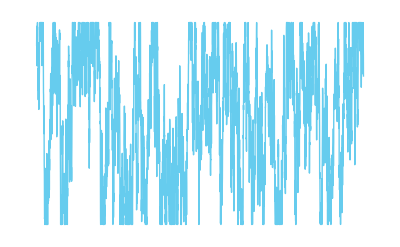

```mathematica
ListPlot[xx,Joined->True,FrameLabel->{t,x}]
```

```mathematica
(*yy0=Sin/@(Range[tt]/13);yy=cut/@(((yy0+1)/2)+RandomVariate[NormalDistribution[0,0.1],tt]);*)
```

```mathematica
step=1/10;
yy=Table[0,{tt}];
ini=RandomReal[{0,1}];
Do[ini=cut[ini+RandomVariate[NormalDistribution[0,step]]];
yy[[t]]=ini
,{t,tt}];
```

```mathematica
x0=0.25;y0=0.25;
cov=DiagonalMatrix[0.004/{lx,ly}];
spt=Table[pr=PDF[MultinormalDistribution[{x0,y0},cov],{xx[[t]],yy[[t]]}]*Sqrt@Det[2*Pi*cov];
RandomChoice[{pr,1-pr}->{1,0}],{t,tt}];
spxy=T[{Pick[xx,spt,1],Pick[yy,spt,1]}];
psp=ListPlot[spxy,Joined->False,PlotStyle->red,PlotMarkers->Auto];
```

```mathematica
plot=Show[{ListPlot[T@{xx,yy},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],AspectRatio->ly/lx,FrameTicks->{{{0,1},None},{{0,1},None}},FrameLabel->{xla,yla}],psp}];
expng["xy_nocover",plot,600];
```

```mathematica
(*zz0=Exp[-Log[(yy0+1)/2]*Log[(xx0+1)/2]];
(*zz0=((yy0+1)/2)/((xx0+1)/2);*)
zz=(*Mod[#,1]&/@*)
cut/@
(zz0+RandomVariate[NormalDistribution[0,0.05],tt]);*)
```

```mathematica
(*fln[x_,y_]:=If[x==-Infinity||y==-Infinity,+Infinity,x*y];SetAttributes[fln,Listable];*)
```

```mathematica
zz0=Exp[-Identity[Log[yy]*Log[xx]]];
(*zz0=((yy0+1)/2)/((xx0+1)/2);*)
zz=(*Mod[#,1]&/@*)
cut/@
(zz0+RandomVariate[NormalDistribution[0,0.05],tt]);
```

```mathematica
(*zz0=xx^2*yy^2;
(*zz0=((yy0+1)/2)/((xx0+1)/2);*)
zz=(*Mod[#,1]&/@*)
cut/@
(zz0+RandomVariate[NormalDistribution[0,0.05],tt]); *)
```

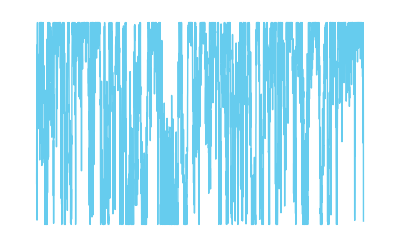

```mathematica
ListPlot[zz,Joined->True,FrameLabel->{t,λ}]
```

```mathematica
(*x0=-0.7;y0=0.6;
spt=Table[pr=Exp[-((xx[[t]]-x0)^2+(yy[[t]]-y0)^2)*50];RandomChoice[{pr,1-pr}->{1,0}],{t,tt}];*)
spxyz=T[{Pick[xx,spt,1],Pick[yy,spt,1],Pick[zz,spt,1]}];

psp=ListPointPlot3D[spxyz,PlotStyle->red];
```

```mathematica
spa=T[{Pick[xx,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red,PlotMarkers->{●,12}];
plot=Show[{ListPlot[T@{xx,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{xla,zla},FrameTicks->{{{0,1},None},{{0,1},None}},AspectRatio->lz/lx],pspa}];
expng["xz_nocover",plot,600];
```

```mathematica
spa=T[{Pick[yy,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red,PlotMarkers->{●,12}];
plot=Show[{ListPlot[T@{yy,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{yla,zla},FrameTicks->{{{0,1},None},{{0,1},None}},AspectRatio->lz/ly],pspa}];
expng["yz_nocover",plot,600];
```

```mathematica
viewpoint={2.76011950196867,-1.775003163456029,0.8252903153274592};
```

```mathematica
plot=Show[{ListPointPlot3D[T@{xx,yy,zz},PlotStyle->Directive[Opacity[0.1],Thin,grey],Axes->True,AxesLabel->{x,y,λ},BoxRatios->{lx,ly,lz},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Ticks->{{0,1},{0,1},{0,1}}]/.Point->Line,psp},ViewPoint->Dynamic[viewpoint]];
expng["xyz_nocover",plot,600];
```

```mathematica
(* now full cover *)
```

```mathematica
zz0=Exp[-Identity[Log[yy]*Log[xx]]];
(*zz0=((yy0+1)/2)/((xx0+1)/2);*)
zz=(*Mod[#,1]&/@*)
cut/@
(zz0+RandomVariate[NormalDistribution[0,0.05],tt]);
```

```mathematica
step=1/10;
zz=Table[0,{tt}];
ini=RandomReal[{0,1}];
Do[ini=cut[ini+RandomVariate[NormalDistribution[0,step]]];
zz[[t]]=ini
,{t,tt}];
```

```mathematica
(*zz0=xx^2*yy^2;
(*zz0=((yy0+1)/2)/((xx0+1)/2);*)
zz=(*Mod[#,1]&/@*)
cut/@
(zz0+RandomVariate[NormalDistribution[0,0.05],tt]); *)
```

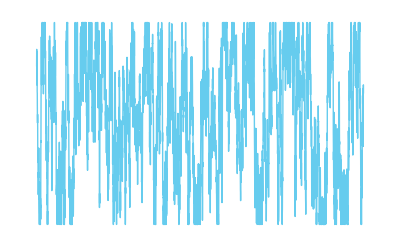

```mathematica
ListPlot[zz,Joined->True,FrameLabel->{t,λ}]
```

```mathematica
(*x0=-0.7;y0=0.6;
spt=Table[pr=Exp[-((xx[[t]]-x0)^2+(yy[[t]]-y0)^2)*50];RandomChoice[{pr,1-pr}->{1,0}],{t,tt}];*)
spxyz=T[{Pick[xx,spt,1],Pick[yy,spt,1],Pick[zz,spt,1]}];

psp=ListPointPlot3D[spxyz,PlotStyle->red];
```

```mathematica
(*x0=-0.7;y0=0.6;
spt=Table[pr=Exp[-((xx[[t]]-x0)^2+(yy[[t]]-y0)^2)*50];RandomChoice[{pr,1-pr}->{1,0}],{t,tt}];*)
spxyz=T[{Pick[xx,spt,1],Pick[yy,spt,1],Pick[zz,spt,1]}];

psp=ListPointPlot3D[spxyz,PlotStyle->red];
```

```mathematica
spa=T[{Pick[xx,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red,PlotMarkers->{●,12}];
plot=Show[{ListPlot[T@{xx,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{xla,zla},FrameTicks->{{{0,1},None},{{0,1},None}},AspectRatio->lz/lx],pspa}];
expng["xz_cover",plot,600];
```

```mathematica
spa=T[{Pick[yy,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red,PlotMarkers->{●,12}];
plot=Show[{ListPlot[T@{yy,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{yla,zla},FrameTicks->{{{0,1},None},{{0,1},None}},AspectRatio->lz/ly],pspa}];
expng["yz_cover",plot,600];
```

```mathematica
viewpoint={2.76011950196867,-1.775003163456029,0.8252903153274592};
```

```mathematica
plot=Show[{ListPointPlot3D[T@{xx,yy,zz},PlotStyle->Directive[Opacity[0.1],Thin,grey],Axes->True,AxesLabel->{x,y,λ},BoxRatios->{lx,ly,lz},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Ticks->{{0,1},{0,1},{0,1}}]/.Point->Line,psp},ViewPoint->Dynamic[viewpoint]];
expng["xyz_cover",plot,600];
```

```mathematica
viewpoint={1.2631965552085476,-3.1198214312952572,0.3479205365310685};
```

```mathematica
Show[{ListPointPlot3D[T@{xx,yy,zz},PlotStyle->Directive[Opacity[0.1],Thin,grey],Axes->True,AxesLabel->{x,y,λ},BoxRatios->1,ViewPoint->Dynamic[viewpoint]]/.Point->Line,psp}]
```

```mathematica
spa=T[{Pick[xx,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red];
Show[{ListPlot[T@{xx,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{x,λ}],pspa},AspectRatio->1]
```

```mathematica
spa=T[{Pick[yy,spt,1],Pick[zz,spt,1]}];
pspa=ListPlot[spa,Joined->False,PlotStyle->red];
Show[{ListPlot[T@{yy,zz},Joined->True,PlotStyle->Directive[Opacity[0.5],grey],FrameLabel->{y,λ}],pspa},AspectRatio->1]
```